```mathematica
ClearAll["Global`*"]; Remove["Global`*"];
```

```mathematica
(* Parameters *)
r1=2; p1=Rationalize[0.4];
r2=3; p2=Rationalize[0.6];
xs = Range[r1+r2+1,25];
```

```mathematica
(* Analytic solution *)
pmfX1[x_] = Binomial[x-1,r1-1] p1^r1(1-p1)^(x-r1);
pmfX2[x_] = Binomial[x-1,r2-1] p2^r2(1-p2)^(x-r2);
```

```mathematica
pmfZ[z_] =∑_(x=r1)^(z-r2) pmfX1[x]pmfX2[z-x];
```

```mathematica
cdfZ[z_] =∑_(x=r1+r2)^z pmfZ[x];
```

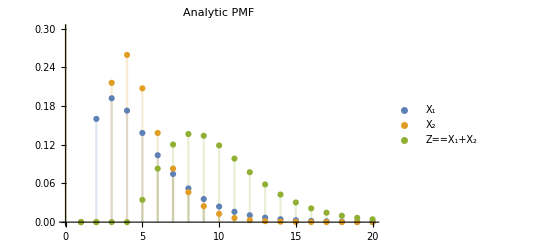

```mathematica
Style[{DiscretePlot[{pmfX1[x], pmfX2[x], pmfZ[x]}, {x, 0, 20},
PlotRange-> {0,0.3},
PlotLabel-> Style["Analytic PMF", FontWeight->Bold, FontColor-> Black],
PlotLegends-> {
ToExpression["X_1",TeXForm,HoldForm],
ToExpression["X_2",TeXForm,HoldForm],
ToExpression["Z=X_1+X_2",TeXForm,HoldForm]}]},ImageSizeMultipliers->{1.5,1.5}]
```

```mathematica
(* Moment generating function *)
M[t_] =(p1 Exp[t])^r1/(1-(1-p1)Exp[t])^r1 (p2 Exp[t])^r2/(1-(1-p2)Exp[t])^r2 ;
```

```mathematica
(* Cumulant generating function *)
K[t_] = Log[M[t]];
K1[t_] =Simplify[D[K[t], t]];
K2[t_] = Simplify[D[K1[t], t]];
K3[t_] = Simplify[D[K2[t], t]];
K4[t_] = Simplify[D[K3[t], t]];
```

```mathematica
(* First order S.P.A. of PMF *)
sHatULim = -Log[1-Min[{p1,p2}]]; (* Upper bound of convergence strip of MGF *)
pmfSPA1[x_]=Module[
{sHat=NSolve[{K1[z]==x,z<sHatULim},z, Reals][[1,1,2]]},
1/(√(2π K2[sHat]))Exp[K[sHat]-x sHat]];
```

```mathematica
(* Second order S.P.A. of PMF *)
pmfSPA2[x_]=Module[
{sHat=NSolve[{K1[z]==x,z<sHatULim},z, Reals][[1, 1, 2]]},
 pmfSPA1[x](1+1/8(K4[sHat]/K2[sHat]^2)-5/24(K3[sHat]/K2[sHat]^(3/2))^2)];
```

```mathematica
(* First order S.P.A. of CDF *)
cdfSPA1[x_]=Module[{x=x,x1=x+1,sHat,w,u,normPdfW,out}, (* increment x to account for strict inequality in SPA CDF (discrete) *)
sHat=NSolve[{K1[z]==x1,z<sHatULim},z, Reals][[1, 1, 2]];
w=Sign[sHat]Sqrt[2sHat x1-2K[sHat]];
u=(1-Exp[-sHat])Sqrt[K2[sHat]];
normPdfW=PDF[NormalDistribution[0,1],  w];
If[Abs[x1-K1[0]]<0.000001,
Evaluate[1/2(cdfSPA1[x-0.1]+cdfSPA1[x+0.1])], (* Removable singularity if X=E[X] - use linear interpolation *)
Evaluate[(CDF[NormalDistribution[0,1], w] + normPdfW(1/w-1/u))]]];
```

```mathematica
trueValues = N[Map[pmfZ, xs]];
spa1Values = Map[pmfSPA1, xs];
spa2Values = Map[pmfSPA2, xs];
```

```mathematica
Grid[Transpose[{Flatten[{"True", trueValues}],Flatten[{"SPA 1st",spa1Values}],Flatten[{"SPA 2nd",spa2Values}]}], Frame-> All]
```

True | SPA 1st | SPA 2nd
0.082944 | 0.0901188 | 0.0824519
0.120269 | 0.125693 | 0.120148
0.136581 | 0.140835 | 0.136561
0.133872 | 0.137072 | 0.133884
0.118909 | 0.121207 | 0.118915
0.0984601 | 0.100052 | 0.0984418
0.0773834 | 0.0784604 | 0.0773392
0.0584337 | 0.0591555 | 0.0583721
0.0427607 | 0.0432457 | 0.0426931
0.0305159 | 0.0308454 | 0.0304516
0.0213383 | 0.0215655 | 0.0212829
0.014673 | 0.0148319 | 0.0146286
0.00995014 | 0.0100623 | 0.00991658
0.00666903 | 0.00674861 | 0.00664472
0.00442583 | 0.00448228 | 0.00440883
0.00291242 | 0.0029523 | 0.00290087
0.00190262 | 0.00193062 | 0.00189495
0.00123512 | 0.00125462 | 0.00123013
0.000797405 | 0.00081087 | 0.000794209
0.000512329 | 0.000521545 | 0.000510309

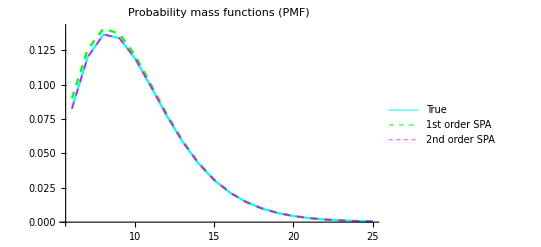

```mathematica
Style[{ListLinePlot[{Thread[{xs, trueValues}],Thread[{xs, spa1Values}],Thread[{xs,spa2Values}]}, PlotLegends ->{"True", "1st order SPA", "2nd order SPA"}, 
PlotStyle->{Directive[Cyan,Thickness[0.004]],Directive[Green, Thickness[0.004],Dashed],Directive[Magenta, Thickness[0.003],Dashed]},PlotLabel-> Style["Probability mass functions (PMF)", FontWeight->Bold, FontColor-> Black]]},ImageSizeMultipliers->{1.5,1.5}]
```

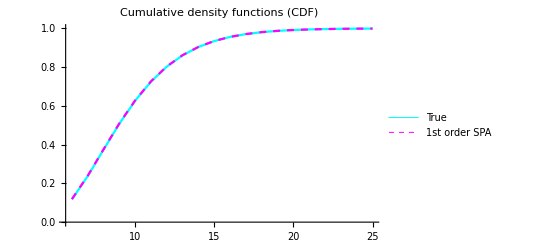

```mathematica
Style[{ListLinePlot[{Thread[{xs, Map[cdfZ, xs]}],Thread[{xs, Map[cdfSPA1, xs]}]}, PlotLegends ->{ "True", "1st order SPA" }, 
PlotStyle->{Directive[Cyan,Thickness[0.004]],Directive[Magenta, Thickness[0.004],Dashed]},
PlotLabel-> Style["Cumulative density functions (CDF)", FontWeight->Bold, FontColor-> Black]]},ImageSizeMultipliers->{1.5,1.5}]
```

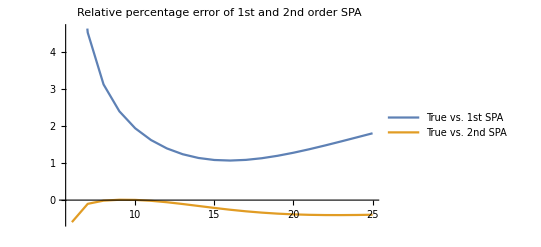

```mathematica
Style[{ListLinePlot[{
Thread[{xs, 100(spa1Values - trueValues)/trueValues}],
Thread[{xs, 100(spa2Values - trueValues)/trueValues}]
},
PlotLegends-> {"True vs. 1st SPA", "True vs. 2nd SPA"},
PlotLabel-> Style["Relative percentage error of 1st and 2nd order SPA", FontWeight-> Bold, FontColor -> Black]]},ImageSizeMultipliers->{1.5,1.5}]
```

```mathematica
Print["Analytic:       Probability of having more than 8 kids: ", N[1-cdfZ[8]]]
Print["Analytic:       Probability of having more than 12 kids: ", N[1-cdfZ[12]]]
Print["1st order SPA:  Probability of having more than 8 kids: ", 1-cdfSPA1[8]]
Print["1st order SPA:  Probability of having more than 12 kids: ", 1-cdfSPA1[12]]
```

Analytic:       Probability of having more than 8 kids: 0.625646

Analytic:       Probability of having more than 12 kids: 0.197022

1st order SPA:  Probability of having more than 8 kids: 0.624017

1st order SPA:  Probability of having more than 12 kids: 0.196042